```mathematica
SetDirectory["/Users/erichegonzales/Projects/Wolfram"]
```

/Users/erichegonzales/Projects/Wolfram

```mathematica
skyline = Import["/Users/erichegonzales/Downloads/manhattanSkyline.jpeg"]
```

-Graphics-

```mathematica
var = RandomVariate[ParetoDistribution[1, 1.5], {10, 10}]
```

{{1.14855,2.03227,2.52343,1.08202,1.16865,2.94745,1.72053,1.65296,1.99659,1.23793},{1.58089,1.56019,1.17391,1.70816,2.99747,1.60132,1.37615,1.02064,1.16736,29.3982},{2.56053,1.07052,6.34527,1.24407,2.42283,1.16413,8.6445,2.3623,1.47913,1.07402},{2.33186,11.8288,13.7162,1.39032,1.12566,1.46927,4.84583,1.825,1.21093,1.92411},{13.0397,1.17009,1.0322,2.6785,1.07446,1.01107,1.58817,1.21966,1.11908,1.61887},{6.81654,2.53076,1.11132,24.2849,1.0633,1.12638,1.17948,2.17407,1.73176,1.79583},{1.78374,1.22988,1.05582,1.11405,9.52888,1.17818,2.27341,1.20076,1.09863,1.05737},{1.48794,2.00557,1.17098,49.9702,1.14807,1.33569,1.06841,1.1062,1.16905,2.32076},{1.74234,5.39613,1.17038,2.72878,2.53692,1.0703,3.0253,2.52054,1.73767,3.07488},{3.5279,55.8563,2.33941,1.39379,1.27047,3.29844,1.47571,1.39019,1.04332,2.16775}}

```mathematica
var2 = RandomVariate[NormalDistribution[2, 0.5], {50, 5}];
```

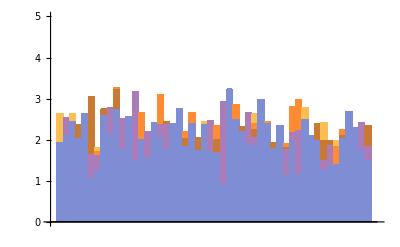
{-Graphics-,-Graphics-}

```mathematica
{BarChart[var2, ChartLayout->"Overlapped", PlotRange->{0, 5}], skylineCropped}
```

```mathematica
skyline3d = Import["../../Downloads/aerialFromSouth.jpeg"]
```

-Graphics-

```mathematica
var3 = RandomVariate[NormalDistribution[3, 0.5], 10]
```

{2.44671,3.18698,3.03051,2.67555,3.12589,2.7843,3.07357,2.82623,3.29522,2.95837}

```mathematica
apts = MapThread[Cuboid[{#1, 0, 0}, {#1+1, 1, #3}]&, {Range[0, 9], Range[0, 9], var3}]
```

{Cuboid[{0,0,0},{1,1,2.44671}],Cuboid[{1,0,0},{2,1,3.18698}],Cuboid[{2,0,0},{3,1,3.03051}],Cuboid[{3,0,0},{4,1,2.67555}],Cuboid[{4,0,0},{5,1,3.12589}],Cuboid[{5,0,0},{6,1,2.7843}],Cuboid[{6,0,0},{7,1,3.07357}],Cuboid[{7,0,0},{8,1,2.82623}],Cuboid[{8,0,0},{9,1,3.29522}],Cuboid[{9,0,0},{10,1,2.95837}]}

```mathematica
Range[0, 9]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
mus = RandomVariate[ParetoDistribution[3, 2], 4]
```

{3.04398,3.00892,6.094,10.2094}

```mathematica
mus = RandomVariate[ParetoDistribution[3, 2], 4]
neighborhoods = 
MapThread[Table[Cuboid[{i, j, 0}, {i+.7, j+.7, RandomVariate[NormalDistribution[#1, 0.5]]}], {i, #2, #3}, {j, #4, #5}]&, {mus, {0, 0, 10, 10}, {9, 9, 19, 19}, {0, 10, 0, 10}, {9, 19, 9, 19}}];
```

{19.9015,4.30483,30.4909,3.41677}

```mathematica
s = RandomVariate[NormalDistribution[1, 1]]
```

0.445367

```mathematica
mu = RandomVariate[ParetoDistribution[1, 2]]
```

2.16531

```mathematica
Mod[4, 2]
```

0

```mathematica
k = 0;
cubes = {};
While[k <= 4,
i = (Mod[k, 2])* 10;
maxi = i+9;
If[k <=2, j = 0, j = 10];
maxj = j+9;
While[ i <= maxi,
s = RandomVariate[NormalDistribution[mu, 1]];
While[j<=maxj,
AppendTo[cubes, Cuboid[{i, j, 0}, {i+s,j+s, s*2}]];
j+=s+.1;
];
j = 0;
i+=s + .1
];
k+=1
]
```

```mathematica
cubes;
```

```mathematica
Graphics3D[cubes,PlotRange->{{0,20},{0,20},{0,20}},Axes->True]
```

-Graphics3D-